## Дифференциальные уравнения

### DSolve и NDSolve

DSolve[eqn,fn,var] точное решение в символьном виде

```mathematica
sol=DSolve[x'[t]==x[t],x[t],t]
```

{{x[t]→ⅇ^t C[1]}}

```mathematica
First[sol] (*первый элемент из списка*)
```

{x[t]→ⅇ^t C[1]}

```mathematica
sol[[1]] (*первый элемент из списка, другая запись*)
```

{x[t]→ⅇ^t C[1]}

```mathematica
x[t] /.First[sol]/.C[1]-> K (*несколько замен по правилам подряд*)
```

ⅇ^t K

```mathematica
x[t] /.First[DSolve[{x'[t]==x[t],x[0]==2},x[t],t]] (*сразу получаем ответ*)
```

2 ⅇ^t

```mathematica
{x[t],y[t]}/.First[DSolve[{x'[t]==2y[t]-x[t],y'[t]==-x[t]+y[t]},{x[t],y[t]},t]] (*система дифф. уравнений*)
```

{C[1] (Cos[t]-Sin[t])+2 C[2] Sin[t],-C[1] Sin[t]+C[2] (Cos[t]+Sin[t])}

```mathematica
(*тонкости*)
```

```mathematica
sol1 = DSolve[x''[t]== -ω^2 x[t], x, t]
```

{{x→Function[{t},C[1] Cos[t ω]+C[2] Sin[t ω]]}}

```mathematica
{x[τ],x'[τ]} /.sol1⟦1⟧ (*заменили обозначение переменной, посчитали производную*)
```

{C[1] Cos[τ ω]+C[2] Sin[τ ω],ω C[2] Cos[τ ω]-ω C[1] Sin[τ ω]}

```mathematica
{x[1.5/ω],x'[1.5/ω]}/.sol1⟦1⟧
```

{0.0707372 C[1]+0.997495 C[2],-0.997495 ω C[1]+0.0707372 ω C[2]}

```mathematica
(*вроде бы все тоже самое*)
```

```mathematica
sol2 = DSolve[x''[t]== -ω^2 x[t], x[t], t]
```

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

```mathematica
x[t] /.sol2⟦1⟧
```

C[1] Cos[t ω]+C[2] Sin[t ω]

```mathematica
x[1.5/ω] /.sol2⟦1⟧ (*не получается *)
```

x[1.5/ω]

```mathematica
x[t] /.sol2⟦1⟧ /.t->1.5/ω (*вышли из положения*)
```

0.0707372 C[1]+0.997495 C[2]

```mathematica
(*скорость тоже не вычисляется*)
```

```mathematica
x'[t]/.sol2⟦1⟧
```

x'[t]

```mathematica
D[x[t]/.sol2⟦1⟧,t] (*а вот так посчитали*)
```

ω C[2] Cos[t ω]-ω C[1] Sin[t ω]

```mathematica
(*В первом случае ответ: вместо x подставлять функцию заданного вида от одного аргумента, который обозначен t 
во втором : вместо x[t] подставлять выражение*)
```

```mathematica
(*переобозначение констант*)
```

```mathematica
sol3 = DSolve[x''[t]== -ω^2 x[t], x, t, GeneratedParameters->a]
```

{{x→Function[{t},a[1] Cos[t ω]+a[2] Sin[t ω]]}}

```mathematica
C=1
```

Set::wrsym: Symbol C is Protected.

1

```mathematica
C[1] = 0
```

Set::write: Tag C in 1 is Protected.

0

```mathematica
a[1] = 0
```

0

```mathematica
x[t] /.sol3
```

{a[2] Sin[t ω]}

```mathematica
DSolve[{x''[t]== -ω^2 x[t], (ω x[0]-x'[0])^2==v^2, ω x[0]+x'[0]==0}, x, t] (* условия на решения чуть более сложного вида*)
```

{{x→Function[{t},(v Cos[t ω]-v Sin[t ω])/(2 ω)]},{x→Function[{t},(-v Cos[t ω]+v Sin[t ω])/(2 ω)]}}

```mathematica
(*решение в специальных функциях*)
```

```mathematica
DSolve[y''[x] - x y[x]==0,y[x],x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
DSolve[z^2 y''[z]+z y'[z]+(z^2-n^2) y[z]==0,y,z]
```

{{y→Function[{z},BesselJ[n,z] C[1]+BesselY[n,z] C[2]]}}

```mathematica
DSolve[ y''[z]+(1-n/z^2) y[z]==0,y,z]
```

{{y→Function[{z},√z BesselJ[1/2 √(1+4 n),z] C[1]+√z BesselY[1/2 √(1+4 n),z] C[2]]}}

```mathematica
(*вроде бы несложно, но *)
```

```mathematica
DSolve[ y''[z]+(1-n/z^n) y[z]==0,y,z]
```

DSolve[(1-n z^-n) y[z]+y''[z]==0,y,z]

0. Найти решение дифференциального уравнения в символьном виде, проверить являются ли найденные функции решениям(и) уравнения, построить график решения и/или фазовый портрет. Исследовать решение в зависимости от параметров
0) y' + y tan(x) = sin(2x), y(0)=2 
1) a y'' + b y' + c y = 0 , y(0)=0, y'(0)=1

1. Исследовать решения уравнение вынужденных колебаний гармонического осциллятора (груз на линейной пружине).
Показать, как изменяются аналитические решения в зависимости от соотношения параметров.
Построить графики решения для перемещения x(t) и скорости x(t) груза, фазовый портрет, а также график зависимости амплитуды колебаний от соотношения частот (аналогичный приведенному ниже). 

m x''(t)+b x'(t)+c (x(t))^2=A cos(ω t) ,
x(0)=x0, x'(0)=v0
 (m,b,c,A,ω>0)  

  -Graphics-

NDSolve[eqns,fn,{var,min,max}] численное решение
Обыкновенные дифф. уравнения
некоторые ДУЧП (параболические и гиперболические)
Граничные задачи для ОДУ
ДУ с запаздывающим аргументом (Delay differential equations)
Гибридные системы (системы с разрывными прав. частями)
Дифф-алгебраические уравнения
Параметрические дифф. уравнения

```mathematica
ndsol1 =NDSolve[{θ''[t]== -Sin[θ[t]],θ[0]==(3π)/4,θ'[0]==0}, θ, {t,0,10}]
```

{{θ→InterpolatingFunction[…]}}

```mathematica
(*решение - интеполяционная функция!*)
```

```mathematica
θ[t]/.ndsol1⟦1⟧
```

InterpolatingFunction[…][t]

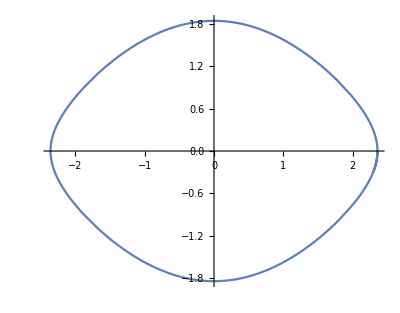

```mathematica
ParametricPlot[Evaluate[{θ[t],θ'[t]}/.ndsol1⟦1⟧],{t,0,10},AspectRatio->Automatic]
```

```mathematica
(*пример работы функции Interpolation*)
```

```mathematica
Table[{t,Sin[t]},{t,0,4 π,π/2}] (*таблица со значениями функции Sin в точках от 0 до 4pi шагом pi/2*)
```

{{0,0},{π/2,1},{π,0},{(3 π)/2,-1},{2 π,0},{(5 π)/2,1},{3 π,0},{(7 π)/2,-1},{4 π,0}}

```mathematica
iFcn=Interpolation[Table[{t,Sin[t]},{t,0,4 π,π/2}]]
```

InterpolatingFunction[…]

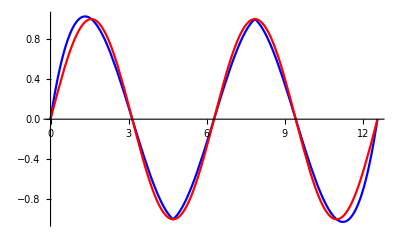

```mathematica
Plot[{iFcn[t],Sin[t]},{t,0,4 π},PlotStyle->{Blue,Red}] (*синяя кривая - интерполяция, красная - sin *)
```

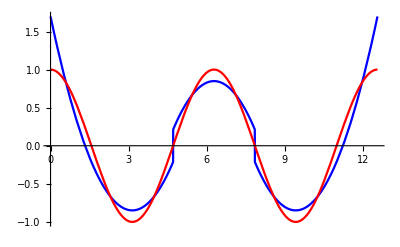

```mathematica
Plot[Evaluate[{D[iFcn[t],t],Cos[t]}],{t,0,4 π},PlotStyle->{Blue,Red}] (*c производными ожидаемо хуже*)
```

```mathematica
(*системы уравнений*)
```

```mathematica
ndsol3 =NDSolve[{ω[t] == θ'[t],ω'[t]== -Sin[θ[t]],θ[0]==(3π)/4,ω[0]==0}, {θ,ω}, {t,0,10}]
```

{{θ→InterpolatingFunction[…],ω→InterpolatingFunction[…]}}

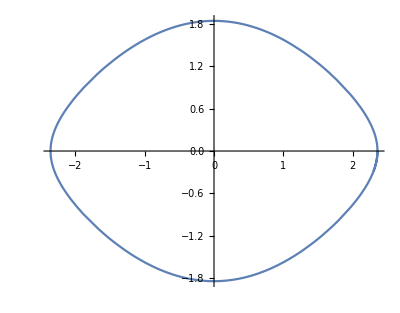

```mathematica
ParametricPlot[Evaluate[{θ[t],ω[t]}/.ndsol3⟦1⟧],{t,0,10},AspectRatio->Automatic]
```

```mathematica
(* система Лоренца*)
```

```mathematica
lorenzEqs = {
		x'[t] == α( -x[t]+y[t]),
		y'[t] == -x[t] z[t] + β x[t] - y[t],
		z'[t] == x[t] y[t] - γ z[t] };
```

```mathematica
(*функция, которая решает систему Лоренца и рисует решение при заданных значениях параметров α, β, γ (values), начальных условиях (ic) и на заданном временном интервале (tmax)*)
```

```mathematica
lorenzPlot[values_,ic_,tmax_]:= ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.NDSolve[Join[lorenzEqs/.values,ic],{x,y,z},{t,0,tmax},MaxSteps->10000]⟦1⟧],{t,0,tmax},PlotPoints->3000]
```

```mathematica
lorenzPlot[{α->10,β->28,γ->8/3},{x[0]==0,y[0]==1,z[0]==-1},30]
```

-Graphics3D-

```mathematica
(*Dsolve vs NDSolve*)
```

```mathematica
ds=DSolve[{y'[x]==y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^x}}

```mathematica
nds=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
```

{{y→InterpolatingFunction[…]}}

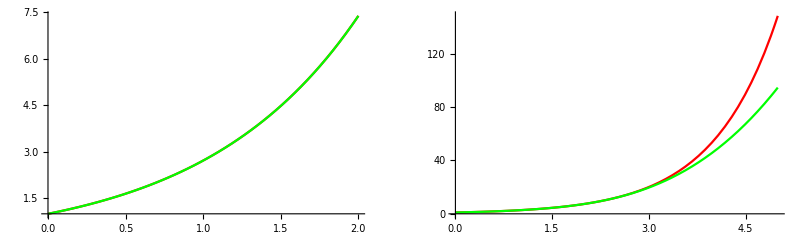

```mathematica
GraphicsRow[{Plot[{y[x]/.ds,y[x]/.nds},{x,0,2},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}],
Plot[{y[x]/.ds,y[x]/.nds},{x,0,5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]}] (*вне области решения NDSolve не совпадает с точным решением *)
```

```mathematica
s=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,20}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

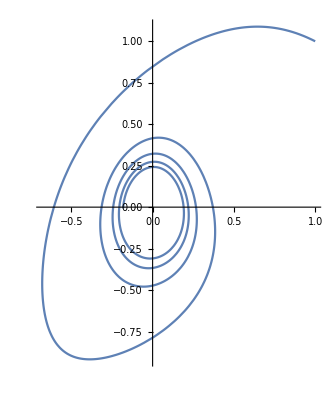

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,20}] (*фазовый портрет*)
```

### Красивые рисунки

```mathematica
tm=700;
```

```mathematica
soln={x[1][t],x[2][t],x[3][t],x[4][t]}/.NDSolve[{x[1]'[t]==-0.002x[1][t],x[2]'[t]==0.4x[1][t]-0.08x[2][t]-x[2][t]x[3][t]^2,x[3]'[t]==-x[3][t]+0.08x[2][t]+x[2][t](x[3][t])^2,x[4]'[t]==0.005x[3][t],x[1][0]==2.5,x[2][0]==0,x[3][0]==0,x[4][0]==0},Table[x[i][t],{i,1,4}],{t,0,tm}]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
m1=700/40;m2=3.3/30;
```

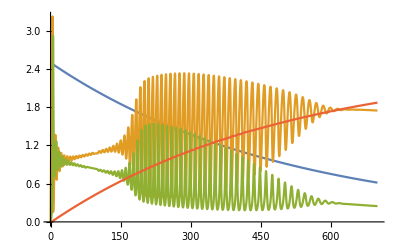

```mathematica
Plot[Evaluate[First[soln]],{t,0,tm}] (*картинка по умолчанию*)
```

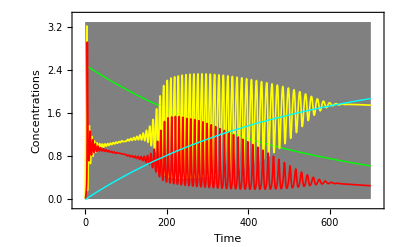

```mathematica
Plot[Evaluate[First[soln]],{t,0,tm},PlotRange->{{-m1,tm+m1},{-m2,3.3+m2}},PlotStyle ->{{Green,Thick},{Yellow,Thickness[0.003]},{Red,Thickness[0.003]},{Cyan,Thick}},FrameLabel ->{"Time","Concentrations"},Frame -> True,Prolog ->{{Thickness[0.002],Gray,Rectangle[{0,0},{tm,3.3}]}},FrameTicks ->{Range[0,700,100],Range[0,3],None,None},PlotRangeClipping -> False] (*заменили цвета линий, добавили названия осей и цветной фон*)
```

```mathematica
(*a damped pendulum:*)
```

```mathematica
pend=x[t]/.First[NDSolve[{x''[t]==-x'[t]-10 Sin[x[t]],x[0]==-14,x'[0]==15},x[t],{t,0,15}]]
```

InterpolatingFunction[…][t]

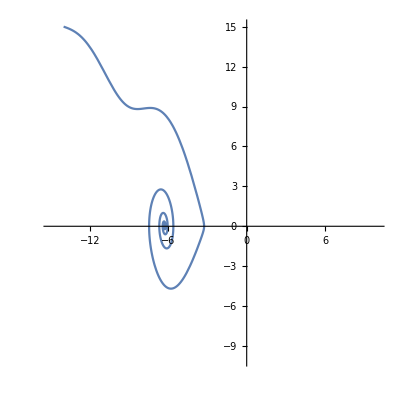

```mathematica
ParametricPlot[Evaluate[{pend,D[pend,t]}],{t,0,15},PlotRange->{{-15,10},{-10,15}}]
```

```mathematica
(*нарисует красиво для разных начальных условий*)
```

```mathematica
Table[{x,-15},{x,-7.6,14,0.8}] (*таблица значений*)
```

{{-7.6,-15},{-6.8,-15},{-6.,-15},{-5.2,-15},{-4.4,-15},{-3.6,-15},{-2.8,-15},{-2.,-15},{-1.2,-15},{-0.4,-15},{0.4,-15},{1.2,-15},{2.,-15},{2.8,-15},{3.6,-15},{4.4,-15},{5.2,-15},{6.,-15},{6.8,-15},{7.6,-15},{8.4,-15},{9.2,-15},{10.,-15},{10.8,-15},{11.6,-15},{12.4,-15},{13.2,-15},{14.,-15}}

```mathematica
initial=Join[Table[{x,15},{x,-14,-7,0.5}],Table[{x,-15},{x,7.6,14,0.8}]]; (*объединили значения на разных интервалах*)
```

```mathematica
pendls=Table[x[t]/.First[NDSolve[{x''[t]==-x'[t]-10 Sin[x[t]],x[0]==iv⟦1⟧,x'[0]==iv⟦2⟧},x[t],{t,0,15}]],{iv,initial}]; (*таблица решений с начальными данными из initials*)
```

```mathematica
(*рисуем, перекрашиваем в цвета из политры Rainbow в зависимости от номера в таблице решения *)
```

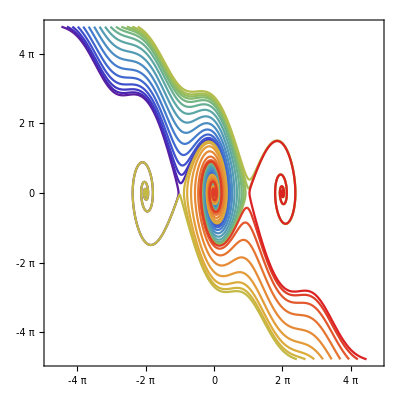

```mathematica
orbits=ParametricPlot[Evaluate[Transpose[{pendls,D[pendls, t]}]],{t,0,15},PlotRange->{{-15,15},{-15,15}},Frame->True,Axes->None,FrameTicks->{{Range[-4 Pi,4 π,2π],None},{Range[-4 Pi,4 π,2π],None}},PlotStyle->Table[{ColorData["Rainbow"][i/24]},{i,24}]]
```

```mathematica
(*меняем только начальное положение*)
```

```mathematica
pendl[iv_]:=x[t]/.First[NDSolve[{x''[t]==-x'[t]-10 Sin[x[t]],x[0]==iv⟦1⟧,x'[0]==iv⟦2⟧},x[t],{t,0,15}]]
```

```mathematica
(*начальное положение считывается с положения курсора*)
```

```mathematica
Manipulate[s=pendl[iv];ParametricPlot[Evaluate[{s,D[s, t]}],{t,0,15},PlotRange->{{-15,15},{-15,15}},Frame->True,Axes->None,FrameTicks->{{Range[-4 Pi,4 π,2π],None},{Range[-4 Pi,4 π,2π],None}},PlotStyle->Thick],{{iv,{1,10}},Locator}]
```

2. Найти численное решение уравнения (системы дифференциальных уравнений) с заданными начальными условиями, если ε - малый параметр, ϵ<<1. Как меняет решение при росте ε (ε ∈ [0, 1])? Сравнить с точным решением при ϵ=0. 

a) Уравнение Дюффинга (колебание груза на нелинейной пружине)
 x''(t)+ 4x(t) +ε  (x(t))^3 ==0, x(0)=1, x'(0)=0 

b) t x'(t)=x+ε y(t), t y'(t)=(2-x) y, x(1)=1, y(1)=1/e

3. Найти двучленное асимптотическое разложение решения уравнения (системы дифференциальных уравнений) с заданными начальными условиями. Сравнить полученное приближенное решение с численным решением системы. ϵ - малый параметр, ϵ<<1. 

a) Уравнение Дюффинга (колебание груза на нелинейной пружине)
 x''(t)+ ω^2 x(t) +ϵ b (x(t))^3 ==0, x(0)=a, x'(0)=0
 
b) x''(t)+ ω^2 x(t) -ϵ b x'(t)^2 x(t) ==0, x(0)=0, x'(0)=v_0

c) t x'(t)=x+ϵ y(t), t y'(t)=(2-x) y, x(1)=1, y(1)=1/e